# 2D First-Passage time

## Drift towards the equilibrium at (x~, y~) = (0, 0) with an absorbing boundary at x~=x~*.

## Write down the nondimensionalized transport eq

```mathematica
FP=λt*D[yt*P[xt, yt], xt]+κt*D[yt*P[xt, yt], yt]-κt*D[xt*P[xt, yt],yt];
```

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-κt, κt}}
B = {{1,0},{0,κt}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-κt,κt}}

{{1,0},{0,κt}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{1/(2 κt)+1/(2 λt)+λt/2,1/(2 λt)},{1/(2 λt),κt/2+1/(2 λt)}}

## Choose the parameter values

```mathematica
λts = {0.5, 0.75, 1.25, 1.5};
κts = {10, 11, 12, 13};
κScale = Flatten[Table[κts^2/2, 4]] (*For scaling the flux to a probability distribtion*)
params = Flatten[Table[{λt->l, κt->k}, {l, λts}, {k, κts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "κt="<>ToString[k], {l, λts},{k, κts}], 1];
products = Table[i*j, {i, λts}, {j, κts}]
```

{50,121/2,72,169/2,50,121/2,72,169/2,50,121/2,72,169/2,50,121/2,72,169/2}

{{λt→0.5,κt→10},{λt→0.5,κt→11},{λt→0.5,κt→12},{λt→0.5,κt→13},{λt→0.75,κt→10},{λt→0.75,κt→11},{λt→0.75,κt→12},{λt→0.75,κt→13},{λt→1.25,κt→10},{λt→1.25,κt→11},{λt→1.25,κt→12},{λt→1.25,κt→13},{λt→1.5,κt→10},{λt→1.5,κt→11},{λt→1.5,κt→12},{λt→1.5,κt→13}}

{{5.,5.5,6.,6.5},{7.5,8.25,9.,9.75},{12.5,13.75,15.,16.25},{15.,16.5,18.,19.5}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+(√(κt-4 λt))/(√κt)),1},{1/2-(√(κt-4 λt))/(2 √κt),1}}

```mathematica
cstar = Flatten[Table[(1/2 (1+(√(κt-4 λt))/(√κt)))^-1/.p, {p, params}]]
```

{1.05573,1.05013,1.04555,1.04174,1.08893,1.07945,1.0718,1.0655,1.17157,1.15038,1.13394,1.12078,1.22515,1.1946,1.17157,1.15354}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = Table[ss[[1,1]]/.p, {p, params}]
ytwidths = Table[ss[[2,2]]/.p, {p, params}]
xywidths = Table[ss[[1,2]]/.p, {p, params}]
```

{1.3,1.29545,1.29167,1.28846,1.09167,1.08712,1.08333,1.08013,1.075,1.07045,1.06667,1.06346,1.13333,1.12879,1.125,1.12179}

{6.,6.5,7.,7.5,5.66667,6.16667,6.66667,7.16667,5.4,5.9,6.4,6.9,5.33333,5.83333,6.33333,6.83333}

{1.,1.,1.,1.,0.666667,0.666667,0.666667,0.666667,0.4,0.4,0.4,0.4,0.333333,0.333333,0.333333,0.333333}

Choose the widest distribution

```mathematica
xtvarChoice=1;
ytvarChoice=4;
xyvarChoice = 1;
```

Initial stds in x~, y~

```mathematica
xtStds = Table[Sqrt[xtwidths[[xtvarChoice]]],Length[params]]
ytStds = Table[Sqrt[ytwidths[[ytvarChoice]]],Length[params]]
```

{1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018}

{2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861,2.73861}

#### Boundary condition at x~* -> y~* = c* x~*. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 20;
xtls=-5*xtStds
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088}

{25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009,25.7009}

{1.05573,1.05013,1.04555,1.04174,1.08893,1.07945,1.0718,1.0655,1.17157,1.15038,1.13394,1.12078,1.22515,1.1946,1.17157,1.15354}

{34.8076,34.6956,34.604,34.5278,35.4717,35.282,35.129,35.003,37.1245,36.7008,36.3719,36.1088,38.196,37.5851,37.1245,36.7638}

```mathematica
icPos =Table[{xt0, c*xt0}, {c, cstar}];
icVar =1.05*{{xtwidths[[xtvarChoice]], xywidths[[xyvarChoice]]},{xywidths[[xyvarChoice]], ytwidths[[ytvarChoice]]}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  P[xtl, yt]==0,
        
    
           P[xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
cellDistances = Table[Min[ytStds]/100, 16]
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}];
```

{{1.365,1.05},{1.05,7.875}}

{0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861,0.0273861}

```mathematica
ytCheckFunc[ytl_, c_]:=c≤ ytl
```

```mathematica
MapThread[ytCheckFunc, {cstar*xt0-5*ytStds, cstar}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

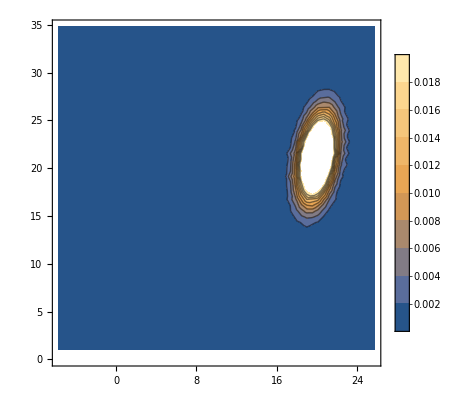

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.02}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxBoundaryCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

General::stop: Further output of NDSolve::femcscd will be suppressed during this calculation.

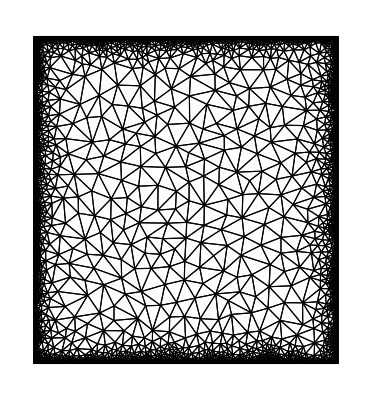

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

```mathematica
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

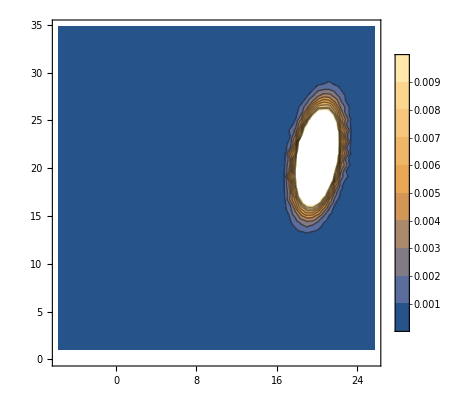

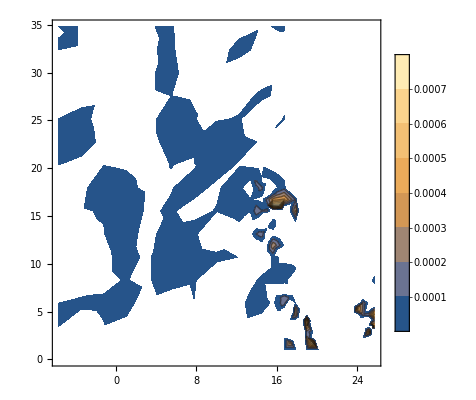

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotRange->{0, 0.01}, PlotLegends->Automatic]
ContourPlot[solsIc0[[toPlot]][xt, yt], {xt, xtls[[toPlot]], xtrs[[toPlot]]}, {yt, ytls[[toPlot]], ytrs[[toPlot]]}, PlotLegends->Automatic, PlotRange->{0, 0.001}]
```

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{fluxXIc0,ytls}])*κScale;
```

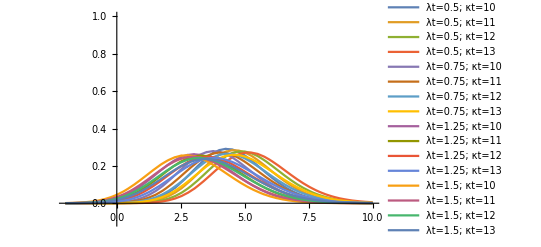

```mathematica
Plot[XIc0, {xt, -2, 10}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {xt, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xtls/2, xtrs/2}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {XIc0*xt, xtls, xtrs}]
secondIc0 = MapThread[IntegFunc, {XIc0*xt*xt, xtls, xtrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.9995080811,0.9994488326,0.9993767807,0.9994539166,0.999912894,0.9998369822,0.9997864429,0.9996908088,1.000339526,1.000235493,1.000164479,1.00004412,1.000625692,1.000610524,1.000272311,1.000230718}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{4.475661284,4.787818085,5.087328894,5.377422342,3.961886759,4.261083493,4.54911047,4.827172142,3.196240008,3.483733398,3.760190597,4.025592612,2.877730005,3.164629929,3.43841517,3.701848263}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{21.9991336,24.99635823,28.06146633,31.19988524,17.81732767,20.39996992,23.05445274,25.77792877,12.58004982,14.64729234,16.78827476,18.98980583,10.73350762,12.62556942,14.58479007,16.610961}

{1.9675897,2.0731562,2.1805511,2.2832142,2.120781,2.2431374,2.3600467,2.4763379,2.3640996,2.510894,2.6492414,2.7844099,2.4521776,2.6106868,2.7620912,2.9072804}

```mathematica
grid = Flatten[Table[{l, s}, {l, λts}, {s, κts}], 1];
params
```

{{λt→0.5,κt→10},{λt→0.5,κt→11},{λt→0.5,κt→12},{λt→0.5,κt→13},{λt→0.75,κt→10},{λt→0.75,κt→11},{λt→0.75,κt→12},{λt→0.75,κt→13},{λt→1.25,κt→10},{λt→1.25,κt→11},{λt→1.25,κt→12},{λt→1.25,κt→13},{λt→1.5,κt→10},{λt→1.5,κt→11},{λt→1.5,κt→12},{λt→1.5,κt→13}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {4,4}];
varArrayIc0 = ArrayReshape[varsIc0, {4,4}];
meanArrayIc0 = ArrayReshape[meansIc0, {4,4}];
diffArrayIc0 = ArrayReshape[diffIc0, {4,4}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{5,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4}, λts}];
yticks = Transpose[{{1, 2, 3, 4}, κts}];
```

```mathematica
varArrayIc0;
meanArrayIc0
```

{{4.475661284,4.787818085,5.087328894,5.377422342},{3.961886759,4.261083493,4.54911047,4.827172142},{3.196240008,3.483733398,3.760190597,4.025592612},{2.877730005,3.164629929,3.43841517,3.701848263}}

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ -0.2,White},{2,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]

ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {4,4}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]

ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
```

-Graphics-

-Graphics-

-Graphics-

#### Check that all s.s. variances have been reached before mean passage

```mathematica
S[A_, B_] := FullSimplify[Integrate[MatrixExp[-A*(t-tp)].B.Transpose[B].MatrixExp[-Transpose[A]*(t-tp)], {tp, 0, t}]];
```

```mathematica
As = {{ 0,λ},{-κ, 1}}
Bs = {{1,0},{0,κ }}
s0[λ_, κ_, t_] = FullSimplify[MatrixExp[-{{ 0,λ},{-κ, 1}}*t].icVar.MatrixExp[-Transpose[{{ 0,λ},{-κ, 1}}]*t]];
```

{{0,λ},{-κ,1}}

{{1,0},{0,κ}}

{{1/(-0.25+1. κ λ)(ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ)))),1/(-0.25+1. κ λ)(-3.18875 Cosh[t]+3.18875 Sinh[t]) (0.392003-2. κ-0.184339 λ+(κ (2.-1.56801 λ)+0.184339 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.0921697 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)])},{1/(-0.25+1. κ λ)(-3.18875 Cosh[t]+3.18875 Sinh[t]) (0.392003-2. κ-0.184339 λ+(κ (2.-1.56801 λ)+0.184339 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.0921697 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)]),1/(-0.25+1. κ λ)(ⅇ^-t κ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(t (-1+√(1-4 κ λ))) (-0.293906+0.293906 √(1-4 κ λ)+κ (1.25-6.3775 κ+0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(-t (1+√(1-4 κ λ))) (-0.293906-0.293906 √(1-4 κ λ)+κ (1.25-6.3775 κ+0.587813 λ+1.25 √(1-4 κ λ))))}}

```mathematica
S0 =%532[[1,1]];
```

1/(-0.25+1. κ λ)(ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ))))

```mathematica
curve =S[As, Bs];
```

{{(((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+√(1-4 κ λ)-2 κ λ (-1+κ λ)))/(1+√(1-4 κ λ))-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ)))/(-1+√(1-4 κ λ))+4 κ λ (1+κ λ) (1-Cosh[t]+Sinh[t]))/(-2+8 κ λ),(ⅇ^(-t (2+√(1-4 κ λ))) (-4 ⅇ^(t (1+√(1-4 κ λ))) κ λ (1+κ λ)+ⅇ^(t (2+√(1-4 κ λ))) (-2+8 κ λ)+ⅇ^t (1-√(1-4 κ λ)+2 κ λ (-1+κ λ))+ⅇ^(t+2 t √(1-4 κ λ)) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ))))/(4 λ (-1+4 κ λ))},{(ⅇ^(-t (2+√(1-4 κ λ))) (-4 ⅇ^(t (1+√(1-4 κ λ))) κ λ (1+κ λ)+ⅇ^(t (2+√(1-4 κ λ))) (-2+8 κ λ)+ⅇ^t (1-√(1-4 κ λ)+2 κ λ (-1+κ λ))+ⅇ^(t+2 t √(1-4 κ λ)) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ))))/(4 λ (-1+4 κ λ)),(κ^2 (-((1-ⅇ^(-t (1+√(1-4 κ λ)))) (3-2 κ λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (-3+2 κ λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+4 (1+κ λ) (1-Cosh[t]+Sinh[t])))/(-2+8 κ λ)}}

```mathematica
toPlotCurve[λ_, κ_, t_]=1.05S0+curve[[1,1]];
```

1/(-0.25+1. κ λ)1.05 (ⅇ^-t λ (-2.5+12.755 κ+1.17563 λ)+ⅇ^(-t (1+√(1-4 κ λ))) (-3.18875+3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ-1.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-3.18875-3.18875 √(1-4 κ λ)+λ (1.25+6.3775 κ-0.587813 λ+1.25 √(1-4 κ λ))))+(((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+√(1-4 κ λ)-2 κ λ (-1+κ λ)))/(1+√(1-4 κ λ))-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+√(1-4 κ λ)+2 κ λ (-1+κ λ)))/(-1+√(1-4 κ λ))+4 κ λ (1+κ λ) (1-Cosh[t]+Sinh[t]))/(-2+8 κ λ)

```mathematica
Manipulate[Plot[{toPlotCurve[λ, κ, t], 1/2+1/(2 κ λ)+(κ λ)/2}, {t, 0, 35}, PlotRange->{0, 35}, GridLines->{{{tfPlot [λ, κ, 8],Red}},None}], {λ, 0.01, 0.5}, {κ, 0.2, 0.45}]
```

```mathematica
tfPlot [λ_, κ_, x0_] := (1/λ)*Log[x0/(2*κ/(1+Sqrt[1-4*λ*κ]))]
```